## Nonlinear observer for harmonic oscillator (Example 7.8)

```mathematica
Clear["Global`*"];
```

Full nonlinear observer

```mathematica
f[L1_,tend_,initval_]:=Module[{eq,eqh,init,inith,x1,x2,xh1,xh2,L2,t},
L2=L1^2/4-Cos[xh1[t]];
eq={x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]};
eqh={xh1'[t]==xh2[t]+ L1(x1[t]-xh1[t]), xh2'[t]==-Sin[xh1[t]]+ L2(x1[t]-xh1[t])};
init={x1[0]==0,x2[0]==initval};   
inith={xh1[0]==xh2[0]==0};
NDSolveValue[{eq, eqh,init,inith},{x1,x2,xh1,xh2},{t,0,tend}]]

tend=14; L1=1.5; initval=1.98; (* choose initval to nearly swing up *){xsol1,xsol2,xhsol1,xhsol2}=f[L1,tend,initval];
```

Graphics & data export

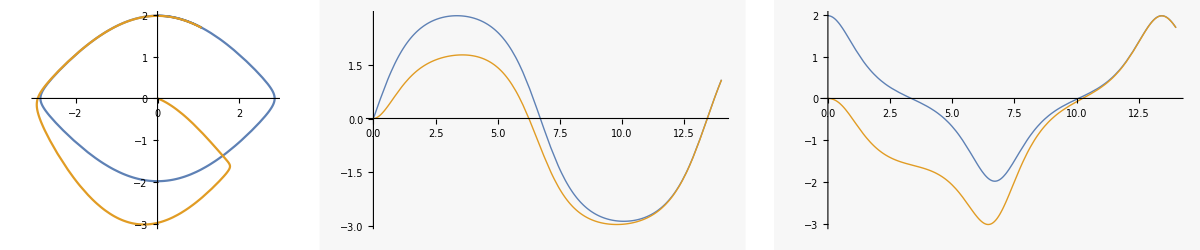

```mathematica
Subscript[p, 1]=ParametricPlot[{{xsol1[t],xsol2[t]},{xhsol1[t],xhsol2[t]}},{t,0,tend}];
Subscript[p, 2]=Plot[{xsol1[t],xhsol1[t]},{t,0,tend}];
Subscript[p, 3]=Plot[{xsol2[t],xhsol2[t]},{t,0,tend}];
GraphicsRow[{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]},ImageSize->{650}]
```

```mathematica
dt=0.01;dat=Table[Through[{xsol1,xsol2,xhsol1,xhsol2}[t]],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumObserver.dat", dat] 
*)
```